```mathematica
Needs["dsvsolve`"];
```

## Input

Edit or simply evaluate the following cell to see the input

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

dSVtShowInput::assm: Assumptions made: {b→0.75,F→0.94,s→0.08}.

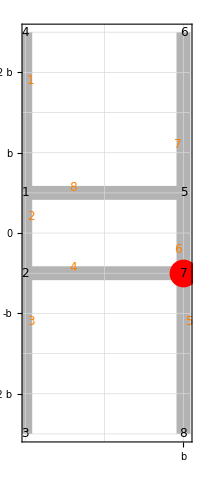

```mathematica
example={$$nodes->{{-b, b/2}, {-b, -1/2*b}, {-b, (-5*b)/2}, {-b, (5*b)/2}, {b, b/2}, {b, (5*b)/2}, {b, -1/2*b}, {b, (-5*b)/2}},
$$edges->{{4, 1}, {1, 2}, {2, 3}, {2, 7}, {7, 8}, {7, 5}, {5, 6}, {1, 5}},
$$thicknesses->s,$$absname->t,$$thname->z,
$$traction->F,$$wheretraction->{b, -b/2},
$$shear->{0, 0}, $$whereshear->{0, 0},
$$bending->{0,0}, $$torsion->0}; dSVtShowInput[example]
```

## Output simbolico

Evaluate the following cell to solve the problem and see the output

```mathematica
sol = {AB, rG, JB, CS, FS, KT, sigma, tau, gobj, details} = dSVtSolve[example];
gsol=dSVtShowOutput[example, sol]
```

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

123456

Evaluate the following cell to print the above output

-Graphics-

-Graphics-

-Graphics-

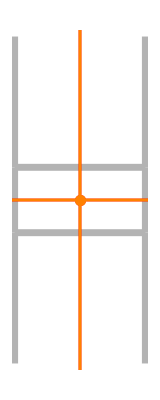

-Graphics-

-Graphics-

```mathematica
CellPrint/@Rest/@Last[sol];
Print/@Cases[gsol,Graphics[___],Infinity];
```

Numerical assumptions for visualization purposes

{b→0.75,F→0.94,s→0.08}

Edge lengths

{{2 b,b,2 b,2 b,2 b,b,2 b,2 b}}

Edges areas Ai

{{2 b s,b s,2 b s,2 b s,2 b s,b s,2 b s,2 b s}}

Total area A

14 b s

Edges static moments sPi

{{{-2 b^2 s,3 b^2 s},{-b^2 s,0},{-2 b^2 s,-3 b^2 s},{0,-b^2 s},{2 b^2 s,-3 b^2 s},{b^2 s,0},{2 b^2 s,3 b^2 s},{0,b^2 s}}}

Static moment sP

{{0,0}}

Edge centroids Gi

{{{-b,(3 b)/2},{-b,0},{-b,-(3 b)/2},{0,-b/2},{b,-(3 b)/2},{b,0},{b,(3 b)/2},{0,b/2}}}

Centroid G

{{0,0}}

Edges Euler inertia tensors IPi

{{{{2 b^3 s,-3 b^3 s},{-3 b^3 s,(31 b^3 s)/6}},{{b^3 s,0},{0,(b^3 s)/12}},{{2 b^3 s,3 b^3 s},{3 b^3 s,(31 b^3 s)/6}},{{(2 b^3 s)/3,0},{0,(b^3 s)/2}},{{2 b^3 s,-3 b^3 s},{-3 b^3 s,(31 b^3 s)/6}},{{b^3 s,0},{0,(b^3 s)/12}},{{2 b^3 s,3 b^3 s},{3 b^3 s,(31 b^3 s)/6}},{{(2 b^3 s)/3,0},{0,(b^3 s)/2}}}}

Total Euler inertia tensor IP

{{(34 b^3 s)/3,0},{0,(131 b^3 s)/6}}

Inertia tensor after translation in the centroid IG

{{(34 b^3 s)/3,0},{0,(131 b^3 s)/6}}

Principal inertia momoments (jI, jII) and associated directions

{{(34 b^3 s)/3,{0,1}},{(131 b^3 s)/6,{1,0}}}

Rotation to principal directions

0

Radii of gyration (ρI, ρII)

{{√(17/21) b,1/2 √(131/21) b}}

Section moduli (WI, WII) and associated directions

{{{(68 b^2 s)/15,(68 b^2 s)/15},{0,1}},{{(131 b^2 s)/6,(131 b^2 s)/6},{1,0}}}

Coefficients {a0,a1,a2} for sigma (= a0 + a1 x1 + a2 x2)

{F/(14 b s),(3 F)/(34 b^2 s),-(3 F)/(131 b^2 s)}

Sigma in principal axis (ξ,η)

((-0.0229008 "η"+0.0882353 "ξ"+0.0714286 b) F)/(b^2 s)

Neutral axis for sigma

{x1→-(17 b)/21+(34 x2)/131}

Intersections of neutral axis with principal axis

{Last[{}],Last[{}]}

Inertia ellipse equation

((21 x1^2)/17+(84 x2^2)/131)/b^2==2

Kern (Convex hull (convex hull has been computed on a numerical instance!)

{{-(17 b)/21,0},{-(17 b)/21,0},{-(17 b)/21,0},{0,-(131 b)/210},{(17 b)/21,0},{(17 b)/21,0},{(17 b)/21,0},{0,(131 b)/210}}

(Shear) Cycles in terms of nodes

{{5,1,2,7,5}}

(Shear) Cycles in terms of edges

{{-8,2,4,6}}

Associated open graph {nodes, edges} (statically undetermined shear)

{{{-b,b/2},{-b,-b/2},{-b,-(5 b)/2},{-b,(5 b)/2},{b,b/2},{b,(5 b)/2},{b,-b/2},{b,-(5 b)/2},{b,b/2}},{{4,1},{1,2},{2,3},{2,7},{7,8},{7,5},{5,6},{1,9}}}

Jourawsky shear on the associated open graph (statically undetermined shear)

{0,0,0,0,0,0,0,0}

Cycles connectivity

{{0},{1},{0},{1},{0},{1},{0},{-1}}

Congruence for statically undetermined shear, matrix ηij

{{(6 b)/s}}

Congruence for statically undetermined shear, vector η0i

{0}

Statically undetermined shear solution: Prandtl function values

{0}

Statically undetermined shear solution: shear fluxes

{0,0,0,0,0,0,0,0}

Shear stress if the shear force is placed in the shear center

{0,0,0,0,0,0,0,0}

Shear stiffness matrix

{{5780/27111,0},{0,17161/29778}}

Shear flexibility matrix

{{27111/5780,0},{0,29778/17161}}

Shear resultants on edges

{{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}}

Shear resultant

{0,0}

Shear center

{{0,0}}

Additional torque due to eccentricity

0

(Torsion) Cycles in terms of nodes

{{5,1,2,7}}

(Torsion) Cycles in terms of edges

{{-8,2,4,6}}

Statically undetermined torsion, congruence matrix ηij

{{(6 b)/s}}

Statically undetermined torsion, vector  2Ω

{4 b^2}

Solution of the statically undetermined torsion

{(2 b s)/3}

Torsion partition over the cycles  Ji/J

{1}

Shear stress due to torsion

{{0,0,0,0,0,0,0,0}}

Torsional inertias Jti

{{{8,2,4,6},(8 b^3 s)/3},{1,(2 b s^3)/3},{3,(2 b s^3)/3},{5,(2 b s^3)/3},{7,(2 b s^3)/3}}

Torsional inertia Jt

8/3 b s (b^2+s^2)

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
Output
```

Output

## Output simbolico

Evaluate the following cell to solve the problem and see the output

```mathematica
sol = {AB, rG, JB, CS, FS, KT, sigma, tau, gobj, details} = dSVtSolve[example];
gsol=dSVtShowOutput[example, sol]
```

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

123456

Evaluate the following cell to print the above output

```mathematica
CellPrint/@Rest/@Last[sol];
Print/@Cases[gsol,Graphics[___],Infinity];
```

Numerical assumptions for visualization purposes

{b→0.75,F→0.94,s→0.08}

Edge lengths

{{2 b,b,2 b,2 b,2 b,b,2 b,2 b}}

Edges areas Ai

{{2 b s,b s,2 b s,2 b s,2 b s,b s,2 b s,2 b s}}

Total area A

14 b s

Edges static moments sPi

{{{-2 b^2 s,3 b^2 s},{-b^2 s,0},{-2 b^2 s,-3 b^2 s},{0,-b^2 s},{2 b^2 s,-3 b^2 s},{b^2 s,0},{2 b^2 s,3 b^2 s},{0,b^2 s}}}

Static moment sP

{{0,0}}

Edge centroids Gi

{{{-b,(3 b)/2},{-b,0},{-b,-(3 b)/2},{0,-b/2},{b,-(3 b)/2},{b,0},{b,(3 b)/2},{0,b/2}}}

Centroid G

{{0,0}}

Edges Euler inertia tensors IPi

{{{{2 b^3 s,-3 b^3 s},{-3 b^3 s,(31 b^3 s)/6}},{{b^3 s,0},{0,(b^3 s)/12}},{{2 b^3 s,3 b^3 s},{3 b^3 s,(31 b^3 s)/6}},{{(2 b^3 s)/3,0},{0,(b^3 s)/2}},{{2 b^3 s,-3 b^3 s},{-3 b^3 s,(31 b^3 s)/6}},{{b^3 s,0},{0,(b^3 s)/12}},{{2 b^3 s,3 b^3 s},{3 b^3 s,(31 b^3 s)/6}},{{(2 b^3 s)/3,0},{0,(b^3 s)/2}}}}

Total Euler inertia tensor IP

{{(34 b^3 s)/3,0},{0,(131 b^3 s)/6}}

Inertia tensor after translation in the centroid IG

{{(34 b^3 s)/3,0},{0,(131 b^3 s)/6}}

Principal inertia momoments (jI, jII) and associated directions

{{(34 b^3 s)/3,{0,1}},{(131 b^3 s)/6,{1,0}}}

Rotation to principal directions

0

Radii of gyration (ρI, ρII)

{{√(17/21) b,1/2 √(131/21) b}}

Section moduli (WI, WII) and associated directions

{{{(68 b^2 s)/15,(68 b^2 s)/15},{0,1}},{{(131 b^2 s)/6,(131 b^2 s)/6},{1,0}}}

Coefficients {a0,a1,a2} for sigma (= a0 + a1 x1 + a2 x2)

{F/(14 b s),(3 F)/(34 b^2 s),-(3 F)/(131 b^2 s)}

Sigma in principal axis (ξ,η)

((-0.0229008 "η"+0.0882353 "ξ"+0.0714286 b) F)/(b^2 s)

Neutral axis for sigma

{x1→-(17 b)/21+(34 x2)/131}

Intersections of neutral axis with principal axis

{Last[{}],Last[{}]}

Inertia ellipse equation

((21 x1^2)/17+(84 x2^2)/131)/b^2==2

Kern (Convex hull (convex hull has been computed on a numerical instance!)

{{-(17 b)/21,0},{-(17 b)/21,0},{-(17 b)/21,0},{0,-(131 b)/210},{(17 b)/21,0},{(17 b)/21,0},{(17 b)/21,0},{0,(131 b)/210}}

(Shear) Cycles in terms of nodes

{{5,1,2,7,5}}

(Shear) Cycles in terms of edges

{{-8,2,4,6}}

Associated open graph {nodes, edges} (statically undetermined shear)

{{{-b,b/2},{-b,-b/2},{-b,-(5 b)/2},{-b,(5 b)/2},{b,b/2},{b,(5 b)/2},{b,-b/2},{b,-(5 b)/2},{b,b/2}},{{4,1},{1,2},{2,3},{2,7},{7,8},{7,5},{5,6},{1,9}}}

Jourawsky shear on the associated open graph (statically undetermined shear)

{0,0,0,0,0,0,0,0}

Cycles connectivity

{{0},{1},{0},{1},{0},{1},{0},{-1}}

Congruence for statically undetermined shear, matrix ηij

{{(6 b)/s}}

Congruence for statically undetermined shear, vector η0i

{0}

Statically undetermined shear solution: Prandtl function values

{0}

Statically undetermined shear solution: shear fluxes

{0,0,0,0,0,0,0,0}

Shear stress if the shear force is placed in the shear center

{0,0,0,0,0,0,0,0}

Shear stiffness matrix

{{5780/27111,0},{0,17161/29778}}

Shear flexibility matrix

{{27111/5780,0},{0,29778/17161}}

Shear resultants on edges

{{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}}

Shear resultant

{0,0}

Shear center

{{0,0}}

Additional torque due to eccentricity

0

(Torsion) Cycles in terms of nodes

{{5,1,2,7}}

(Torsion) Cycles in terms of edges

{{-8,2,4,6}}

Statically undetermined torsion, congruence matrix ηij

{{(6 b)/s}}

Statically undetermined torsion, vector  2Ω

{4 b^2}

Solution of the statically undetermined torsion

{(2 b s)/3}

Torsion partition over the cycles  Ji/J

{1}

Shear stress due to torsion

{{0,0,0,0,0,0,0,0}}

Torsional inertias Jti

{{{8,2,4,6},(8 b^3 s)/3},{1,(2 b s^3)/3},{3,(2 b s^3)/3},{5,(2 b s^3)/3},{7,(2 b s^3)/3}}

Torsional inertia Jt

8/3 b s (b^2+s^2)

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## Caratteristiche geometriche della sezione

```mathematica
valori={F->Quantity[2*10^4,"Kilonewtons"],b->Quantity[14,"Centimeters"],s->Quantity[2,"Centimeters"],σ0->Quantity[20,"Kilonewtons"/"Centimeters"^2]};
A=Last[Last[sol][[4]]];
{{Iy,Iyx},{Ixy,Ix}}=Last[Last[sol][[10]]];
Print["Area = ",A,"=",A/.valori//N//(NumberForm[#1,3]&)];
Print["Ix = ",Ix,"=",Ix/.valori//N//(NumberForm[#1,3]&)];
Print["Iy = ",Iy,"=",Iy/.valori//N//(NumberForm[#1,3]&)];
Print["Ixy = ",Ixy,"=",Ixy/.valori//N//(NumberForm[#1,3]&)];
```

Area = 14 b s=392. cm^2

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

Ix = (131 b^3 s)/6=120000. cm^4

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

Iy = (34 b^3 s)/3=62200. cm^4

Ixy = 0=0.

## Tensione normale

```mathematica
{a0,a1,a2}=Last[Last[sol][[16]]];
σ[x_,y_]=a0+-a1*x-a2*y;
```

```mathematica
Print["σ_z(x,y)=",σ[x,y],"=",σ[x,y]/.valori//N//(NumberForm[#1,3]&)]
```

σ_z(x,y)=F/(14 b s)-(3 F x)/(34 b^2 s)+(3 F y)/(131 b^2 s)=x (-12.3 kN/cm^3)+y (3.18 kN/cm^3)+119. kN/cm^2

## Punti e valori di massima sollecitazione normale

```mathematica
xmax=b;ymax=-5 b/2;
xmin=-b;ymin=5/2b;
```

```mathematica
σmax=σ[xmax,ymax];
σmin=σ[xmin,ymin];
```

```mathematica
Print["σ_max=",σmax,"=",σmax/.valori//N//(NumberForm[#1,3]&)]
Print["σ_min=",σmin,"=",σmin/.valori//N//(NumberForm[#1,3]&)]
```

σ_max=-(2309 F)/(31178 b s)=-123. kN/cm^2

σ_min=(6763 F)/(31178 b s)=362. kN/cm^2